```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
S2=0.00035^2π;
```

```mathematica
Svstn5silicaold=(16 kB T^2 α^2 L^3)/(π κ)(π/(2 √2 b)(Sinh[β]-Sin[β])/(Cosh[β]-Cos[β]))((S E0)/(M ω^2 L-S E0))^2/.b->β/(√2 π)/.β->√((2ω)/(κ/(ρ Cv)))L/.{kB->1.38 10^-23,T->300,α->5.1*10^(-7),L->0.30,κ->1.38*S2,ρ->2200*S2,S->S2,Cv->1.64 10^6/2200,ω->2π f,E0->7.2*10^10,M->40/4};
Pold=LogLogPlot[√Svstn5silicaold,{f,1,10000},PlotRange->{10^-30,10^-11}];
```

```mathematica
Svstn5silica=(8 kB T^2 α^2 L^3)/(2π*π^2 κ)π^2/(4ϕ)(Sinh[2ϕ]-Sin[2ϕ])/(Cosh[2ϕ]-Cos[2ϕ])Abs[(η^4(4 ϕ^4-η^4))/((4 ϕ^4+η^4)^2)]((S E0)/(M ω^2 L-S E0))^2/.{ϕ->√(ω/(2κ/(ρ Cv)))L,η->√((ρ ω^2)/(S E0))L}/.{kB->1.38 10^-23,T->300,α->5.1*10^(-7),L->0.30,κ->1.38*S2,ρ->2200*S2,S->S2,Cv->1.64 10^6/2200,ω->2π f,E0->7.2*10^10,M->40/4};
P0=LogLogPlot[√Svstn5silica,{f,1,10000},PlotRange->{10^-30,10^-11},PlotStyle->Hue[.3]];
```

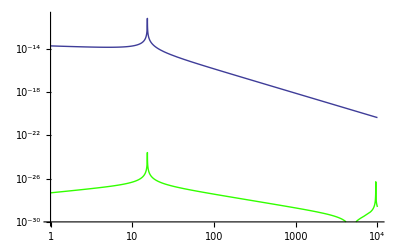

```mathematica
Show[Pold,P0]
```

```mathematica
S1=0.0016^2π/4;Svstn5sap1=(8 kB T^2 α^2 L^3)/(2π*π^2 κ)π^2/(4ϕ)(Sinh[2ϕ]-Sin[2ϕ])/(Cosh[2ϕ]-Cos[2ϕ])Abs[(η^4(4 ϕ^4-η^4))/((4 ϕ^4+η^4)^2)]((S E0)/(M ω^2 L-S E0))^2/.{ϕ->√(ω/(2κ/(ρ Cv)))L,η->√((ρ ω^2)/(S E0))L}/.{kB->1.38 10^-23,T->18,α->5.6*10^(-9),L->0.35,κ->0.032,ρ->0.008,Cv->0.69,ω->2π f,E0->4.0*10^(11),M->23/4,S->S1};
P3=LogLogPlot[√Svstn5sap1,{f,1,10000},PlotRange->{10^-28,10^-11},PlotStyle->Hue[.1]];
```

```mathematica
Svstn5sap300K=(8 kB T^2 α^2 L^3)/(2π*π^2 κ)π^2/(4ϕ)(Sinh[2ϕ]-Sin[2ϕ])/(Cosh[2ϕ]-Cos[2ϕ])Abs[(η^4(4 ϕ^4-η^4))/((4 ϕ^4+η^4)^2)]((S E0)/(M ω^2 L-S E0))^2/.{ϕ->√(ω/(2κ/(ρ Cv)))L,η->√((ρ ω^2)/(S E0))L}/.{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->23/4,S->S1};
P4=LogLogPlot[√Svstn5sap300K,{f,1,10000},PlotRange->{10^-28,10^-11},PlotStyle->Hue[.7]];
```

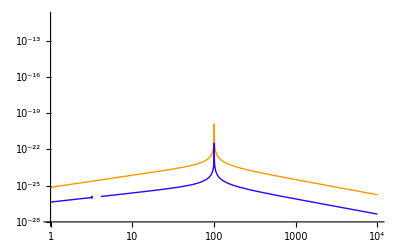

```mathematica
Show[P3,P4]
```

## 7. Data output

```mathematica
logDataOutput[filename_String, X_, {imin_, imax_}] :=
  Module[{strm},
    strm = OpenWrite[filename];
    Do[
      Do[
        Module[{},
          Map[writeList[strm, #] &, { x , X} /. x -> (10^i) 10^ j];
          writeListn[strm];
          ],
        {i, 0.001, 1, 0.001}
        ],
      {j, imin, imax}
      ];
    Close[strm];
    ]
```

```mathematica
writeList[strm_, dat_] :=
  WriteString[strm, ToString[FortranForm[dat]], " "];
```

```mathematica
writeListn[strm_] :=
  WriteString[strm, "\n"];
```

```mathematica
logDataOutput["vstn10sap20K.dat",√Abs[Svstn5sap1]*2*2/300/3000/.{f->x},{0,3}]
```

```mathematica
logDataOutput["vstn10sap300K.dat",√Svstn5sap300K*2*2/300/3000/.{f->x},{0,3}]
```

```mathematica
logDataOutput["vstn10silica4.dat",√Svstn5silica*2*2/1000/4000/.{f->x},{0,3}]
```